```mathematica
Mag={};
For[l=1,l≤400,l++,
out=Import["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Magnetic Profile 8-mags\\Bx_Average_8Mags.txt",{"Lines",l}];
(*otp="{"<>out<>"}";
otp=StringReplace[otp,{"e" :> "*10^"}];
otp=StringReplace[otp,{"\t" :> ","}];
mtp=ToExpression[otp];
Mag=Join[Mag,{mtp[[2]]}];*)
mtp=ToExpression[out];
Mag=Join[Mag,{mtp}];
];
```

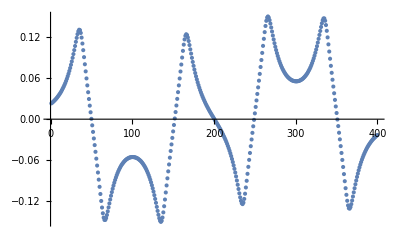

```mathematica
ListPlot[Mag]
```

```mathematica
For[ii=Nx+1.ii≤ Nx+NxM,ii++,
Mag[[ii]]=0.5;
];
```

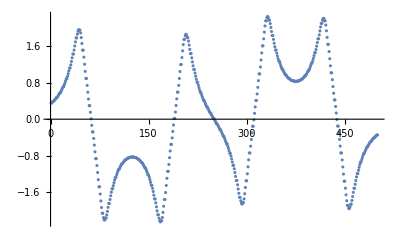

```mathematica
(*Currently MagΔ is being used*)
MagΔ=Table[g*Mag[[Ceiling[ii*Length[Mag]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
ListPlot[{MagΔ}]
```

```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=250-25;
NxM=50;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw*0;
tsw=4.0;
μ=0.0;
g=15;
B=2Δ;

(*tϕ=ts/200;*)
tϕ1=0.4*ts;
tϕ2=ts;
αϕ=0.0;
θ1=0.0π;
θM=0.0π;
θ2=0.0 π;
```

```mathematica
i1=150;
i2=380;
spread=1;
MagΔ=Table[g*Mag[[Ceiling[ii*Length[Mag]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
MagΔA=Table[-6 ⅇ^(-(i-i1)^2/(spread*3000)),{i,1,500}]+Table[5 ⅇ^(-(i-i1)^2/(spread*1000)),{i,1,500}]-Table[-6 ⅇ^(-(i-i2)^2/(spread*3000)),{i,1,500}]-Table[5 ⅇ^(-(i-i2)^2/(spread*1000)),{i,1,500}];
MagΔB=Table[2 ⅇ^(-(i-250)^2/1500),{i,1,500}];
```

```mathematica
MagΔAt=-Table[HeavisideTheta[-i+Nx+0.1],{i,1,2Nx+NxM}]+Table[HeavisideTheta[i-NxM-Nx+0.1],{i,1,2Nx+NxM}];
MagΔBt=Table[HeavisideTheta[i-Nx+0.1]-HeavisideTheta[i-NxM-Nx+0.1],{i,1,2Nx+NxM}];
```

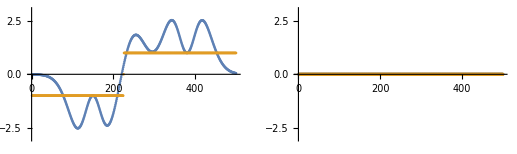

```mathematica
GraphicsRow[{ListPlot[{MagΔA+MagΔB Cos[θM],MagΔAt+MagΔBt Cos[θM]},PlotRange->{-3,3}],ListPlot[{MagΔB Sin[θM],MagΔBt Sin[θM]},PlotRange->{-3,3}]}]
```

```mathematica
(*MagΔA=MagΔAt;
MagΔB=MagΔBt;*)
```

```mathematica
H[ϕ_,θM_]:=Block[{Hsp},
ϵ0=2ts Cos[Pi/(2Nx+NxM+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0+MagΔB[[i]] Sin[θ1],{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0-MagΔB[[i]] Sin[θ1],{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->Table[MagΔA[[i]]+MagΔB[[i]] Cos[θ1],{i,1,Nx}],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->Table[MagΔA[[i]]+MagΔB[[i]] Cos[θ1],{i,1,Nx}],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0+MagΔB[[Nx+i]] Sin[θM],{i,1,NxM}],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0-MagΔB[[Nx+i]] Sin[θM],{i,1,NxM}],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->Table[MagΔA[[Nx+i]]+MagΔB[[Nx+i]]Cos[θM],{i,1,NxM}],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->Table[MagΔA[[Nx+i]]+MagΔB[[Nx+i]] Cos[θM],{i,1,NxM}],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0+MagΔB[[Nx+NxM+i]] Sin[θ2],{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0-MagΔB[[Nx+NxM+i]] Sin[θ2],{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->Table[MagΔA[[Nx+NxM+i]]+MagΔB[[Nx+NxM+i]] Cos[θ2],{i,1,Nx}],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->Table[MagΔA[[Nx+NxM+i]] +MagΔB[[Nx+NxM+i]] Cos[θ2],{i,1,Nx}],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0},{HM1,HMM,HM2},{0,H2M,H22}}]];

Hsp
];
```

```mathematica
H0=H[0.,θM];
{e0,ψ0}=Transpose[Sort[Transpose[Eigensystem[H0,-10]]]];
```

```mathematica
e0
```

{-0.20801,-0.200616,-0.199705,-0.00976374,-9.14493×10^-7,9.14493×10^-7,0.00976374,0.199705,0.200616,0.20801}

```mathematica
eϕ={};
elϕ=Table[{},{n,1,10}];
For[ϕ=0,ϕ≤4π,ϕ+=0.1,


Hsp=H[ϕ,θM];


etp=Sort[Eigenvalues[Hsp,-10]];
For[n=1,n≤Length[etp],n++,
elϕ[[n]]=Join[elϕ[[n]],{{ϕ,etp[[n]]}}]
];
If[π<ϕ<3π,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2+1]]+etp[[Length[etp]/2+2]]}}];
,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2-1]]+etp[[Length[etp]/2]]}}];
];


];


Iϕ={};
IϕM={};
For[ϕi=2,ϕi≤Length[eϕ],ϕi++,
Iϕ=Join[Iϕ,{{eϕ[[ϕi,1]],(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])}}];
IϕM=Join[IϕM,{Re[(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])]}];
];
```

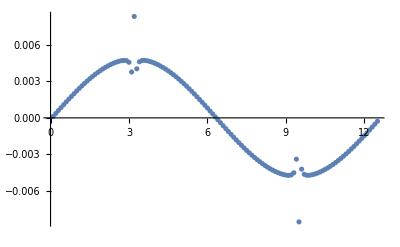

```mathematica
ListPlot[Re[Iϕ],PlotRange->All]
```

```mathematica
a=SessionTime[];
Iθ={};
Imax={};
For[θM=0.0,θM≤2π,θM+=0.01 π,
eϕ={};
elϕ=Table[{},{n,1,10}];
For[ϕ=0,ϕ≤4π,ϕ+=0.1,


(*Full Wire*)
Hsp=H[ϕ,θM];



etp=Sort[Eigenvalues[Hsp,-10]];
For[n=1,n≤Length[etp],n++,
elϕ[[n]]=Join[elϕ[[n]],{{ϕ,etp[[n]]}}]
];
If[π<ϕ<3π,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2+1]]+etp[[Length[etp]/2+2]]}}];
,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2-1]]+etp[[Length[etp]/2]]}}];
];


];

Iϕ={};
IϕM={};
For[ϕi=2,ϕi≤Length[eϕ],ϕi++,
Iϕ=Join[Iϕ,{{eϕ[[ϕi,1]],(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])}}];
IϕM=Join[IϕM,{Re[(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])]}];
];

Iθ=Join[Iθ,{Iϕ}];
Imax=Join[Imax,{{θM,Max[IϕM]}}];
Print[{θM,Max[IϕM]}];
];
```

{0.,0.00696306}

{0.0314159,0.00693007}

{0.0628319,0.00690376}

{0.0942478,0.00688419}

{0.125664,0.00687137}

{0.15708,0.00686524}

{0.188496,0.00686567}

{0.219911,0.00687248}

{0.251327,0.00688544}

{0.282743,0.00690426}

{0.314159,0.00692858}

$Aborted

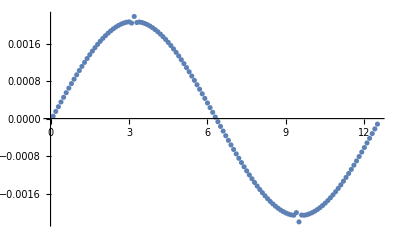

```mathematica
ListPlot[Re[Iθ[[1]]],PlotRange->All]
```

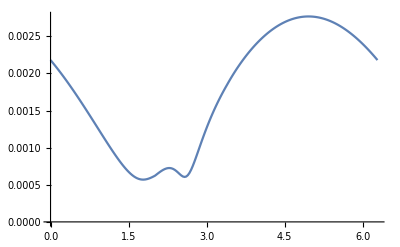

```mathematica
ListPlot[Imax,Joined->True]
```